#### params

```mathematica
Δ=5*10^-3;0.005;
σ=0.01;
α=0.001;
ϕ=0.001;
γ=10;
κ=50;
ε=0.005;
Υ=Δ+ε;
χ=0.02;
tiltλ=50/300;
λ=N[50/300];


Ν=10;(*Total Amt*)
T=300;(*Total Time*)
```

```mathematica
(*Market Impact Cost*)
c[q_]:=α*q;
```

```mathematica
(*Target Schedule*)
IS[t_]:=Ν*(1-Sinh[χ*(T-t)]/Sinh[χ*T])
```

#### eqs

```mathematica
ω[t_,q_]:=ⅇ^(-κ*(Υ+c[Ν-q])*(Ν-q))/;t==T
ω[t_,q_]:=Exp[-κ*ϕ*NIntegrate[(Ν-IS[u])^2,{u,t,T}]]/;q==Ν
```

尝试解析解 建议告辞

```mathematica
eqs=(D[ω[t,q],t]-κ*ϕ*(q-IS[t])^2 ω[t,q]+ⅇ^-1 λ ω[t,q+1])*(ω[t,q]-ⅇ^(-κ*Υ)ω[t,q+1])==0
```

(ω[t,q]-0.606531 ω[t,1+q]) (-0.05 (q-10 (1-0.00495753 Sinh[0.02 (300-t)]))^2 ω[t,q]+0.0613132 ω[t,1+q]+ω^(1,0)[t,q])==0

数值解尝试
Do it backwards

```mathematica
m = {{1,2},{1, 2}};
m[[All,-1]]={3,4};
m
```

{{1,3},{1,4}}

```mathematica
fdmSolver[t_,nt_,q_]:=
Module[
{time=N@Subdivide[0,t,nt],
dt,
mat,
idxTrigger,
trigger
},
dt=First@Differences@time;
mat=ConstantArray[0,{q+1,Length[time]}];
mat[[-1]]=Table[ω[i,q],{i,time}];(*Q terminal condition*)
mat[[All,-1]]=Table[ω[t,i],{i,0,q}];(*T*)
trigger=ConstantArray[0,{q+1, Length[time]}];
(*trigger[[;;,-1]]=ConstantArray[1,q+1];*)
(*from t+dt to t*)
Do[
mat[[1;;-2,idxT]]=
mat[[1;;-2,idxT+1]]-
κ*ϕ*dt*
Thread[
Times[
Power[Range[0,q-1]-IS[time[[idxT+1]]],2],
mat[[1;;-2,idxT+1]]]]
+ⅇ^-1*λ*dt*mat[[2;;-1,idxT+1]];
idxTrigger=Boole[Thread[Less[mat[[1;;-2,idxT]], mat[[2;;-1,idxT]]*ⅇ^(-κ*Υ)]]];
AppendTo[idxTrigger,0];
trigger[[;;,idxT]]=idxTrigger;
mat[[1;;-2,idxT]]=MapThread[Max,{mat[[1;;-2,idxT]],ⅇ^(-κ*Υ)*mat[[2;;-1,idxT]]}];
,{idxT,Range[Length[time]-1,1,-1]}];
{mat,trigger}
]
```

```mathematica
mat=fdmSolver[T,3000,10];
```

```mathematica
mat2 = fdmSolver[T,3000,10];
```

```mathematica
{mat3,trigger} = fdmSolver[T,3000,10];
```

```mathematica
findTrigger[triggerMat_,time_]:=
time[[DeleteCases[Table[
With[{row=triggerMat[[idxQ]]},
SelectFirst[
Range[Length@row],
row[[#]]==1&]],{idxQ,Length@triggerMat}],_Missing]]]
```

```mathematica
Length@trigger
```

11

```mathematica
moSignals=findTrigger[trigger,N@Subdivide[0,T,3000] ]
```

{4.1,10.1,16.9,24.8,34.3,46.2,62.2,86.4,137.1,299.9}

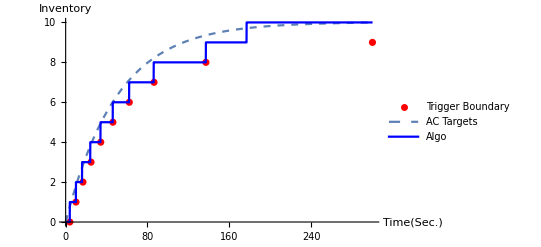

```mathematica
Show[
ListPlot[Transpose[{moSignals,Range[0,Length[moSignals]-1]}],PlotStyle->Red,PlotLegends->{"Trigger Boundary"}],
Plot[IS[i],{i,0,300},PlotStyle->Dashed,PlotLegends->{"AC Targets"}],
ListLinePlot[inv,PlotStyle->Blue,PlotLegends->{"Algo"}],
PlotRange->All,AxesLabel->{"Time(Sec.)","Inventory"}]
```

Find the optimal depth
δ(t,q) = 1/κ+h(t,q)-h(t,q+1)

```mathematica
optDepth[ω_]:=Module[{δ},
δ=ConstantArray[0,Dimensions[ω]];
Do[δ[[i]]=1/κ+1/κ*Log[ω[[i]]]-1/κ*Log[ω[[i+1]]],{i,1, Length[δ]-1}];
δ
]
```

```mathematica
filledPr[δ_]:=ⅇ^(-κ*δ)
```

```mathematica
optDepth[mat3]
```

{{0.0140235,0.0138401,0.0136606,0.0134849,2994,-0.0094777,-0.00951075,-0.009},9,{1}}
 |  |  |  |

#### Price Dynamics

```mathematica
S0=100
```

100

```mathematica
𝒫=TransformedProcess[S0+σ*(up[t]-down[t]),{up\[Distributed]PoissonProcess[γ],down\[Distributed]PoissonProcess[γ]},t];
```

```mathematica
data = RandomFunction[𝒫,{0,T,.1},1]
```

TemporalData[…]

```mathematica
TWAP[price_]:=MovingMap[Mean,price,price["PathLength"],None]
```

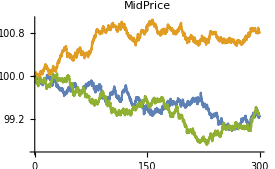
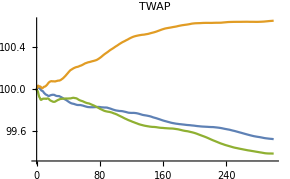

```mathematica
With[{data = RandomFunction[𝒫,{0,T,0.1},3]},
{ListLinePlot[data,PlotRange->All,PlotLabel->"MidPrice"], ListLinePlot[TWAP[data],PlotLabel->"TWAP"]}]
```

```mathematica
data = RandomFunction[𝒫,{0,T,.1},1]
moSignals;
data;
loDepth=optDepth[mat3];
```

TemporalData[…]

```mathematica
timeLine =N@Subdivide[0,300,3000];
```

```mathematica
dt=First@Differences@timeLine
```

0.00333333

```mathematica
midPrice=Last@Transpose[First@Normal[data]];
```

```mathematica
midPrice[[1]]
```

100.

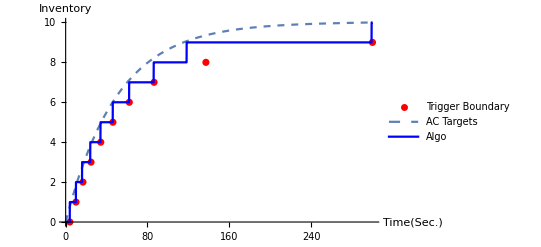

```mathematica
data = RandomFunction[𝒫,{0,T,.1},1];
midPrice=Last@Transpose[First@Normal[data]];
{inv,cash}=Module[
{inventory,
money,
curInv,
curTime,
depth,
isFilled,
isMO},
inventory=ConstantArray[0,3002];
money=ConstantArray[0,3002];
Do[
curInv=inventory[[i]];
curTime=timeLine[[i]];
(*If[inventory[[i]]== 10,Break[]];*)
depth=loDepth[[curInv+1]][[i]];
isFilled=RandomReal[1]<λ*ⅇ^(-κ*depth)*dt;
isMO=Ceiling[moSignals[[curInv+1]]]== Ceiling[curTime];
If[isFilled||isMO,inventory[[i]]+=1;money[[i]]+=midPrice[[i]]];
If[isFilled,money[[i]]+=depth ];
If[isMO,money[[i]]-=Υ];
inventory[[i+1]]=inventory[[i]];
money[[i+1]]=money[[i]];
If[inventory[[i]]== 10,inventory[[i;;-1]]=10;money[[i;;-1]]=money[[i]];Break[]];
,{i,1,3001}];
{Transpose[{timeLine,inventory[[;;-2]]}],money[[;;-2]]}];

Show[
ListPlot[Transpose[{moSignals,Range[0,Length[moSignals]-1]}],PlotStyle->Red,PlotLegends->{"Trigger Boundary"}],
Plot[IS[i],{i,0,300},PlotStyle->Dashed,PlotLegends->{"AC Targets"}],
ListLinePlot[inv,PlotStyle->Blue,PlotLegends->{"Algo"}],
PlotRange->All,AxesLabel->{"Time(Sec.)","Inventory"}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

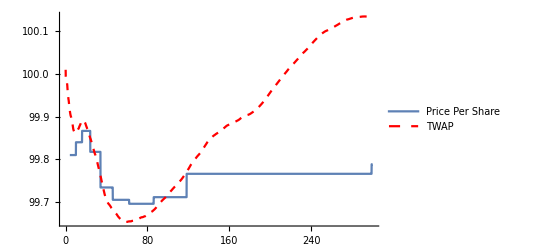

```mathematica
Show[ListLinePlot[DeleteCases[Transpose[{timeLine,cash/Last@Transpose@inv}],{_,Indeterminate}],PlotLegends->{"Price Per Share"}],ListLinePlot[TWAP[data]+Υ,PlotStyle->{Dashed,Red},PlotLegends->{"TWAP"}],PlotRange-> All,AxesOrigin-> {0,Min[TWAP[data]]}]
```

```mathematica
AC=Table[IS[i],{i,timeLine}];
```

```mathematica
diff=Differences[AC];
```

```mathematica
amt=PrependTo[diff,First@AC];
```

```mathematica
money2=FoldList[Plus,amt*(midPrice-Υ)];
```

```mathematica
ACtwap=Transpose[{timeLine,money2/AC}]
```

{{0.,99.99},{0.1,99.96},{0.2,99.965},2995,{299.8,99.7655},{299.9,99.7655},{300.,99.7655}}
 |  |  |  |

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

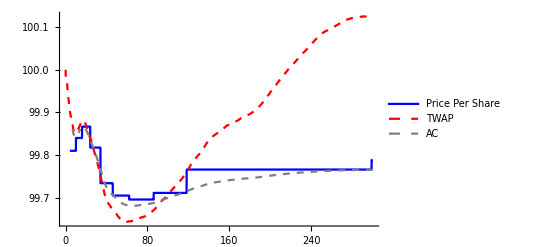

```mathematica
Show[ListLinePlot[DeleteCases[Transpose[{timeLine,cash/Last@Transpose@inv}],{_,Indeterminate}],PlotStyle->Blue,PlotLegends->{"Price Per Share"}],ListLinePlot[TWAP[data],PlotStyle->{Dashed,Red},PlotLegends->{"TWAP"}],
ListLinePlot[ACtwap,PlotStyle->{Dashed,Gray},PlotLegends->{"AC"}],
PlotRange-> All,AxesOrigin-> {0,99.2}]
```